```mathematica
(*Math 227A Homework 2*)
```

```mathematica
(*Zachary DeStefano
15247592
Due October 7 2016*)
```

```mathematica
(*Part 1A*)
```

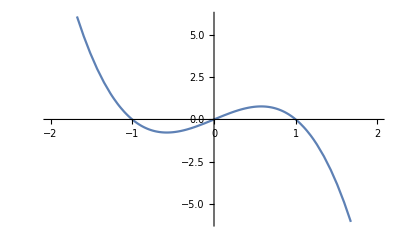

```mathematica
Plot[2y-2y^3,{y,-2,2}]
```

```mathematica
(*Steady States at y=-1, y=0, y=1
y=-1 is stable
y=0 is unstable
y=1 is stable*)

(*Evident from graph as well as fact that f'(y)=2-6y^2 so that
f'(1)=f'(-1)=-4 < 0 so those are stable
and f'(0)=2 > 0 so that one is unstable*)
```

```mathematica
(*I will choose the following initial values for the sample solutions:
Initial Value 1 is y(0) = 1.5
Initial Value 2 is y(0) = 0.5
   Initial Value 3 is y(0) = -0.5
Initial Value 4 is y(0) = -1.5 *)
```

```mathematica
prob1Ainit1 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==1.5},y,{t,0,20}];
```

```mathematica
prob1Ainit2 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==.5},y,{t,0,20}];
```

```mathematica
prob1Ainit3= NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==-.5},y,{t,0,20}];
```

```mathematica
prob1Ainit4 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==-1.5},y,{t,0,20}];
```

```mathematica
(*Here is the graph of sample solutions*)
```

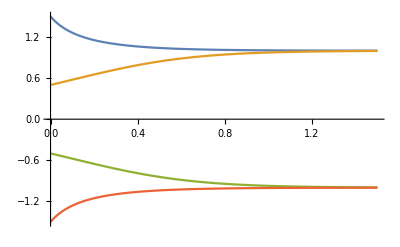

```mathematica
Plot[{prob1Ainit1[t],prob1Ainit2[t],prob1Ainit3[t],prob1Ainit4[t]},{t,0,1.5}]
```

```mathematica
(*Problem 1B*)
(*Steady state if e^(-y)=0 or sin(y)=0
First condition will never happen
sin(y)=0 if y=n*Pi for any integer n*)
(*It holds that f'(y)=e^(-y)(cos(y)-sin(y)) *)
(*Here is verification*)
D[Exp[-y]*Sin[y],y]
```

ⅇ^-y Cos[y]-ⅇ^-y Sin[y]

```mathematica
(*Steady states occur at n*Pi
e^(-y)>0 everywhere so we care about the sign of the other term
If y=2*n*Pi for integer n then cos(y)=1 so f'(y)>0 making those steady states unstable
If y=(2*n+1)*Pi for integer n then cos(y)=-1 so f'(y)<0 making those steady states stable *)
```

```mathematica
(*Here are the initial values that I chose:
y(0) = Pi/4
y(0) = 5Pi/4
y(0) = -Pi/4
y(0) = -5Pi/4*)
```

```mathematica
prob1Binit1 = NDSolveValue[{y'[t]==Exp[-y[t]]*Sin[y[t]],y[0]==Pi/4},y,{t,0,40}];
```

```mathematica
prob1Binit2 = NDSolveValue[{y'[t]==Exp[-y[t]]*Sin[y[t]],y[0]==5*Pi/4},y,{t,0,40}];
```

```mathematica
prob1Binit3 = NDSolveValue[{y'[t]==Exp[-y[t]]*Sin[y[t]],y[0]==-Pi/4},y,{t,0,40}];
```

```mathematica
prob1Binit4 = NDSolveValue[{y'[t]==Exp[-y[t]]*Sin[y[t]],y[0]==-5*Pi/4},y,{t,0,40}];
```

```mathematica
(*Here is the log linear graph of sample solutions*)
```

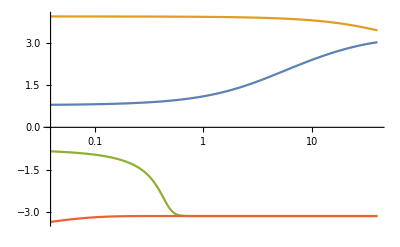

```mathematica
LogLinearPlot[{prob1Binit1[t],prob1Binit2[t],prob1Binit3[t],prob1Binit4[t]},{t,0,40}]
```

```mathematica
(*Problem 2*)
(*Need a function with zeros at 0,1,2,3. For simplicity I will try a polynomial*)
(*One possibility is the form f(y)=Ky(y-1)(y-2)(y-3) *)
(*Here I am computing f'(y) to get info about steady states*)
Expand[D[KK*y(y-1)(y-2)(y-3),y]]
```

-6 KK+22 KK y-18 KK y^2+4 KK y^3

```mathematica
fPrime[y_]:=-6 KK+22 KK y-18 KK y^2+4 KK y^3
```

```mathematica
(*Here I am computing f'(y) at the steady state points*)
```

```mathematica
{fPrime[0],fPrime[1],fPrime[2],fPrime[3]}
```

{-6 KK,2 KK,-2 KK,6 KK}

```mathematica
(*As long as K>0 the properties are satified,
thus every function f(y)=Ky(y-1)(y-2)(y-3) where K>0
satisfies our requirements*)
```

```mathematica
(*Problem 3A*)
```

```mathematica
(*Here are four graphs showing both functions*)
```

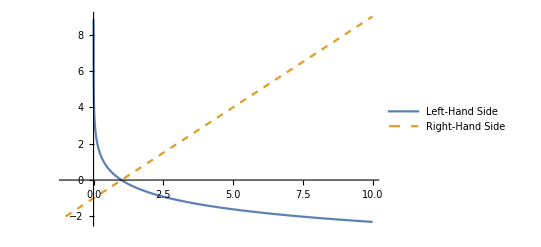

```mathematica
Plot[{-1*Log[y],y-1},{y,-1,10},PlotLegends->{"Left-Hand Side","Right-Hand Side"},PlotStyle->{Thick,Dashed}] (* r=-1 *)
```

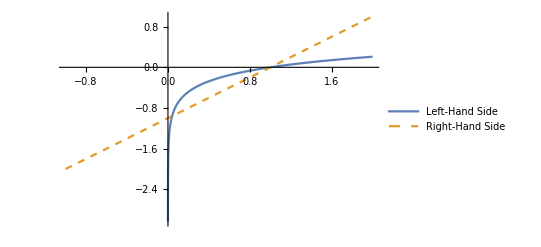

```mathematica
Plot[{0.3*Log[y],y-1},{y,-1,2},PlotLegends->{"Left-Hand Side","Right-Hand Side"},PlotStyle->{Thick,Dashed}] (* r=0.3 *)
```

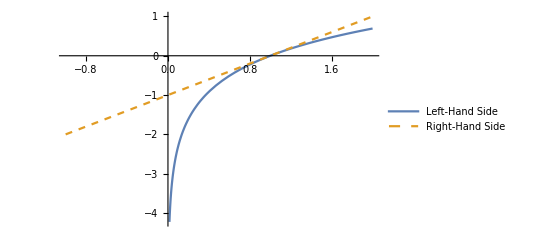

```mathematica
Plot[{Log[y],y-1},{y,-1,2},PlotLegends->{"Left-Hand Side","Right-Hand Side"},PlotStyle->{Thick,Dashed}] (* r=1 *)
```

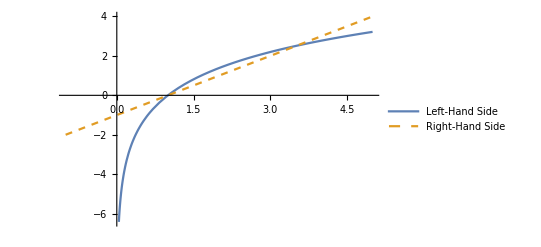

```mathematica
Plot[{2*Log[y],y-1},{y,-1,5},PlotLegends->{"Left-Hand Side","Right-Hand Side"},PlotStyle->{Thick,Dashed}] (* r=2 *)
```

```mathematica
(* At the points where the two graphs intersect, it holds that y'=0 so the intersection points will be the steady states and that holds for any value of r *)
(*It appears for large r, there are two steady states. 
At r=1 there is one steady state. 
Between 0 and 1 there appear to be two steady states. 
For r<0 there appears to be one steady state. 
This is Saddle Node Bifurcation*)
```

```mathematica
(*If y=1, the ln(y)=0 so the value of r is irrelevant*)
```

```mathematica
(*Problem 3B*)
(*Equation is now the following 
u'=-r ln(u+1) + u   
*)
(*Problem 3C*)
(* If we assume that ln(u+1) = u - (1/2)u^2 then when expanding the part b equation using that assumption we have
u' = -r (u - (1/2)u^2 ) + u
u' = -r*u + (1/2)r*u^2 + u  (1)
When you expand the part c equation you end up with
u' = (r/2)u( -2 + 2/r + u)
u' = u( -r + 1 + r*u/2)
u' = -r*u + u + r*u^2/2   (2)
Equation (1) matches equation (2) above so the given equation for u' is valid*)
```

```mathematica
(*Since (-r+1)*(2/r) is a constant just like mu, our system will have very similar behavior around r=1. 
At r=1 and mu=0 the only difference is a constant factor. They both have a single steady state. 
For r>1 the zeros are at 0 and a positive number, just like for mu<0.
For r<1 the zeros are at 0 and a negative number, just like for mu>0.
Both also have a parabolic shape pointing upward, so the first zero is a stable steady state and the second zero is an unstable steady state*)
```

```mathematica
(*Problem 4*)
```

```mathematica
(*For large positive and negative values, y' will be positive. 
The quadratic equation 1+r*y+y^2 has a discriminant of r^2-4
Meaning that if |r|<2 there are no real roots so y' is positive everywhere. 
If r=2 or r=-2 then there is one unstable steady state at y=-1 and y=1 respectively
If |r|>2 there are two steady states at (-r-sqrt(r^2-4))/2 and(-r+sqrt(r^2-4))/2
			The first one is stable and the second one is unstable respectively
This is an example of Saddle Node Bifurcation*)
```

```mathematica
yPrimeFunc[r_]:=1+r*y+y^2;
```

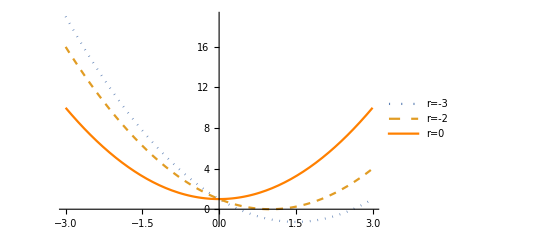

```mathematica
(*This shows the phase diagram for 
r=-3 (two steady states), 
r=-2 (one steady state), and 
r=2 (no steady states)*)
Plot[{yPrimeFunc[-3],yPrimeFunc[-2],yPrimeFunc[0]},{y,-3,3},PlotLegends->{"r=-3","r=-2","r=0"},PlotStyle->{Dotted,Dashed,Orange}]
```

```mathematica
(*It holds that f'(y)=r+2y
For a given r value, the two steady state y values are described by
y1(r) = (-r+sqrt(r^2-4))/2
y2(r) = (-r-sqrt(r^2-4))/2

For y1 it holds that r+2y = sqrt(r^2-4) ≥ 0 so that branch is unstable
For y2 it holds that r+2y = -sqrt(r^2-4) ≤ 0 so that branch is stable 

The bifurcation points occur when r+2y=0 thus (r,y) is equal to (-2,1) and (2,-1)

The plot below shows the stable and unstable branches as well as the bifurcation points as black dots*)
```

```mathematica
prob4Plot = Plot[{(-r+Sqrt[r^2-4])/2,(-r-Sqrt[r^2-4])/2},{r,-6,6}, PlotStyle->{Dashed,Thick},AxesLabel->{r,y}, PlotLegends->{"Unstable","Stable"}];
```

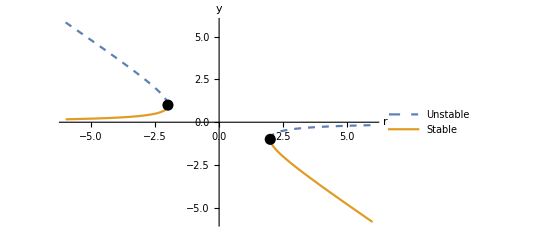

```mathematica
Show[prob4Plot,Graphics[{PointSize[0.02],Point[{-2,1}]}],Graphics[{PointSize[0.02],Point[{2,-1}]}]]
```

```mathematica
(*Problem 5*)
```

```mathematica
prob5Func[r_]:=y*(r-Exp[y])
```

```mathematica
(*For large positive values of y it holds that r won't matter as -y*e^(y) will be a large negative number
For large negative values of y it holds that e^(y) is near zero thus the graph will be similar to r*y
So it r<0 and y negative then y' will be positive, but if r>0 and y negative then y' will be negative *)
```

```mathematica
(*The steady states will occur when y=0 or r=e^y
If r≤0 then there will only be one steady state at y=0 and it will be stable
If r>0 then there will be two steady states at y=0 and y=ln(r). The lower one is unstable and the higher value is stable. 
In the case of r=1 there is one steady state at y=1 and it is unstable.*)
```

```mathematica
(*This is Transcritical Bifurcation*)
```

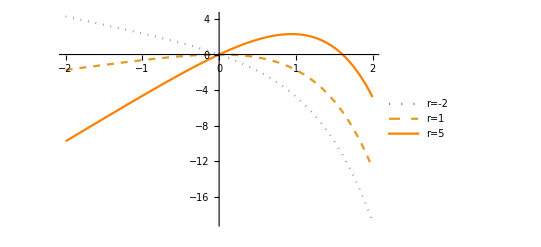

```mathematica
Plot[{prob5Func[-2],prob5Func[1],prob5Func[5]},{y,-2,2},PlotLegends->{"r=-2","r=1","r=5"},PlotStyle->{Dotted,Dashed,Orange}]
```

```mathematica
(*It holds that f'(y)=y(-e^y)+(r-e^y)= r - e^y - y*e^y

For the y=0 bifurcation branch it holds that f'(y)=r-1 
so f'(y)<0 for r<1 (stable part) and f'(y)≥0 for r≥1 (unstable part)

For the r=e^y branch it tholds that f'(y)=-y*e^y so since e^y>0 for all values, it holds that f'(y)<0 for y>0 (stable part) and f'(y)≥0 for y<0 (unstable part)

The Bifurcation Point occurs when (r,y) is equal to (1,0) and is given a black dot below*)
```

```mathematica
prob5Plot = Plot[{Piecewise[{{0,r<1},{Log[r],r≥1}}],Piecewise[{{Log[r],r<1},{0,r≥1}}]},{r,-5,5},AxesLabel->{r,y},PlotLegends->{"Stable","Unstable"},PlotStyle->{Thickness[0.025],{Thickness[0.015],Dashed}}];
```

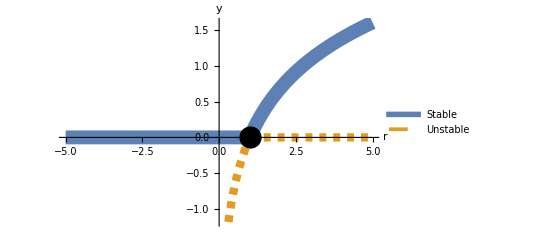

```mathematica
Show[prob5Plot,Graphics[{PointSize[0.04],Point[{1,0}]}]]
```

```mathematica
(*Problem 6*)
```

```mathematica
(*It holds that our equation is y(1 + r/(1+y^2) )=0 so either y=0 or 1 + r/(1+y^2)=0. 
In the later case we can manipulate it to be 
y^2=-(r+1) so it must hold that r<-1 for a root to exist. 
For r<-1 we have three roots: 
y = -sqrt(-r-1) 0 sqrt(-r-1) and they are unstable stable and unstable respectively
For r≥-1 we have an unstable root at y=0

This is Pitch Fork Bifurcation*)
```

```mathematica
prob6Func[r_]:=y+r*y/(1+y^2)
```

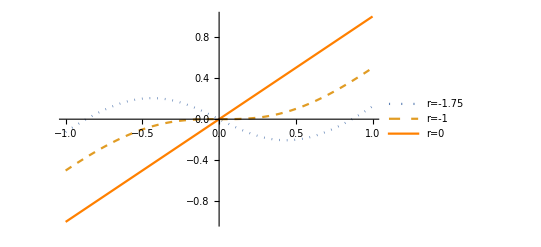

```mathematica
Plot[{prob6Func[-1.75],prob6Func[-1],prob6Func[0]},{y,-1,1},PlotLegends->{"r=-1.75","r=-1","r=0"},PlotStyle->{Dotted,Dashed,Orange}]
```

```mathematica
D[y+r*y/(1+y^2),y]
```

1-(2 r y^2)/((1+y^2)^2)+r/(1+y^2)

```mathematica
(*It thus holds that f'(y) = 1-r( (y^2-1) / (1+y^2)^2 ) *)
```

```mathematica
(* The branches of the graph are y=0 and y^2=-(r+1) 

If y=0 then f'(y)=1+r so if r<-1 the branch is stable but if r≥-1 the branch is unstable

If y^2=-(r+1) then f'(y) = 1 - r( (-r - 2)/r^2 ) = 1 + (r+2)/r = 2(r+1)/r, thus since r≤-1 it holds that f'(y)≥0 hence the branches are unstable

f'(y)=0 in our branches only when r=-1 thus
the Bifurcation Point is (r,y)=(-1,0)
which is given a black dot below*)
```

```mathematica
prob6Plot = Plot[{Piecewise[{{0,r<-1},{Sqrt[-(r+1)],r≥ -1}}],Piecewise[{{-Sqrt[-(r+1)],r<-1},{0,r≥-1}}],Piecewise[{{Sqrt[-(r+1)],r<-1}}]},{r,-5,5},AxesLabel->{r,y},PlotLegends->{"Stable","Unstable","Unstable"},PlotStyle->{Thickness[0.025],{Thickness[0.015],Dashed},{Thickness[0.015],Dashed}}];
```

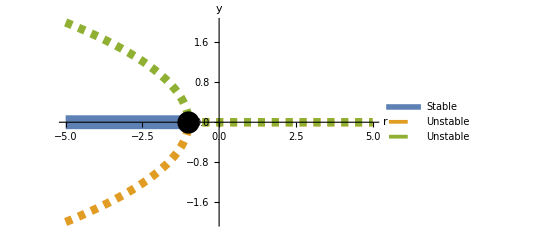

```mathematica
Show[prob6Plot,Graphics[{PointSize[0.04],Point[{-1,0}]}]]
```

```mathematica
(*Extra Problem*)
```

```mathematica
(*Show that y' = y^(1/3) and y(0)=0 has more than one solution*)
```

```mathematica
(*After doing separation of variables, 
we have y^(-1/3) dy = dt. After integrating we have
(3/2) y^(2/3) = t + C
If we assume y(0)=0 then it holds that C=0. 

After rearranging our solution is
y^2 = (2t/3)^3

The positive and negative square root of the right hand side are both solutions, hence there is more than one solution*)

(*Additionally, the function y(t)=0 satisfies both properties and is thus an additional solution*)
```